# Method 1: Genetic Algorithm

### Metric:

Loss metric is non-infinite lifetime for nontrivial solutions. The best lifetime in general is to have a persistent solution and a slow moving glider which are separated enough to live for a long time before colliding. This gives fairly trivial long-living creatures like such:

```mathematica
-Graphics-;
```

So the loss is a combination of lifetime and a maximum separation constraint.

```mathematica
LargestGap[l_]:=Max[Length/@Select[Split[l],First[#]==0&],0]
Lifetime[list_]:=Module[{seen=CreateDataStructure["HashSet", {0}], o=list, count=0, gap=0, gapsum=0},
While[
seen["Insert", FromDigits[o, 2]]&&count<10000,
count++;
o=CellularAutomaton[{20,{2,1},2}, {o, 0}, {{{1}}}];
gap=Max[gap, LargestGap[o]];
];
If[count==10000, 0,count]
]
Loss[list_]:=Module[{seen=CreateDataStructure["HashSet", {0}], o=list, count=0, gap=0},
While[
seen["Insert", FromDigits[o, 2]]&&count<10000,
count++;
o=CellularAutomaton[{20,{2,1},2}, {o, 0}, {{{1}}}];
gap=Max[gap, LargestGap[o]];
];
If[count==10000, 10000 -count+(gap/5)^4, -count+(gap/5)^4]
]
```

### Genetic Algorithm:

```mathematica
RandomFlip[list_]:=BitXor[list, UnitVector[Length[list], RandomInteger[{1, Length[list]}]]]
RandomFlips[n_][list_]:=Nest[RandomFlip, list, n]
```

```mathematica
ParallelSortBy[list_, func_]:=With[{cache=Association@ParallelTable[elem->func[elem], {elem, list}]}, SortBy[list, cache]]
```

```mathematica
RepeatedTiming[ParallelSortBy[Range[100], (Pause[0.01];#^2)&]]
```

{0.102989,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}}

```mathematica
GeneticOptimize[loss_, norig_, numpoints_:100, minpoints_:10, steps_:100]:=Module[
{points=RandomInteger[{0, 1}, {100,norig}], stdout=PrintTemporary[""],minloss, n=norig},

Do[
points=ParallelSortBy[points, loss];
minloss=loss[points[[1]]];
points=Join[points,Join@@ParallelTable[Table[RandomFlip[point], {i, Ceiling[numpoints/minpoints]}], {point, points[[;;minpoints]]}]][[;;numpoints]];
points=First/@GatherBy[points, Lifetime];

If[RandomReal[]>0.95,
n+=1;
points=Table[Append[point, 0], {point, points}]];
If[RandomReal[]>0.95,
n+=1;
points=Table[Prepend[point, 0], {point, points}]];

NotebookDelete[stdout];stdout=PrintTemporary["Step ",step, "/", steps, " | ", Length[points], " points with length ",n," and minimum loss ", minloss];,
{step, steps}];
points=ParallelSortBy[points, loss];
points[[1]]
]
```

### Tests

```mathematica
Timing[l=GeneticOptimize[N@*Loss,100]]
```

{74.0217,{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,0,0,1,1,0,1,1,1,0,0,0,1,1,1,1,0,0,0,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,1,0,1,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,0,1,1,0,0,1,0,0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0}}

```mathematica
Lifetime[l]
ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {l, 0}, %+15]]
```

84

-Graphics-

Other interesting Ones:

```mathematica
-Graphics--Graphics-;
```

### Conclusions:

From what I’ve seen, the genetic algorithm seems to often get stuck in local minima. I’ve tried differentiation techniques like the GatherBy step in the genetic algorithm, but it doesn’t seem to help much. This doesn’t seem like a promising approach for finding persistent solutions rather than just long-living solutions. When allowing for infinite-lifespan solutions, the algorithm seems to converge only on very small infinite solutions, which can be just as easily found by random search. This is in contrast to the sometimes 60-bit wide persistent solutions that have been found.

# Method 2: Gradient Descent

### Code20 Continuous

If code20 could be represented as  a continuous function, then it can undergo gradient descent for the largest final solution. This can be found by interpolating through the code20 rule to get a continuous function.

One easy way to do it is to simply interpolate some few logic gates, and construct code20 from there:

```mathematica
NOT[x_]:=1-x
AND[x_, y_]:=x y

OR[x_, y_]:=NOT[AND[NOT[x], NOT[y]]]
XOR[x_, y_]:=AND[NOT[AND[x, y]], OR[x, y]]

(* a small representation of code20 applied to neighborhood (a, b, c, d, e) *)
code20=XOR[XOR[a, XOR[b, XOR[c, XOR[d, e]]]], OR[a, OR[b, OR[c, OR[d, e]]]]]
```

```mathematica
Code20Single=FunctionCompile[Function[{Typed[a, "Real64"], Typed[b, "Real64"], Typed[c, "Real64"], Typed[d, "Real64"], Typed[e, "Real64"]},

With[{x=((1-(1-(1-a) (1-b) (1-c) (1-d) (1-e)) (1-a (1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))) (1-(1-a) (1-(1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))))) (1-(1-a) (1-b) (1-c) (1-d) (1-e) (1-(1-a (1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))) (1-(1-a) (1-(1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e))))))))))}, 

Return[x];(1.0000908039820193*Exp[20(N[x]-1/2)]/(1+Exp[20(N[x]-1/2)]))-0.0000453978687024344

]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
WindowsPaddedZero[list_]:=With[{l=Join[{0, 0}, list, {0, 0}]}, Table[l[[i;;i+4]], {i, Length[l]-4}]]
Code20Row[list_]:=Code20Single@@@WindowsPaddedZero[list]
```

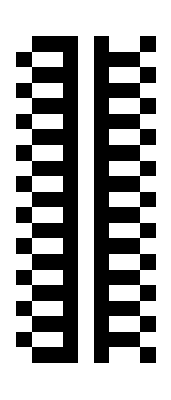

```mathematica
ArrayPlot[NestList[Code20Row,Prepend[{1, 1, 1, 0, 1, 0, 0, 1}, 0],20]]
```

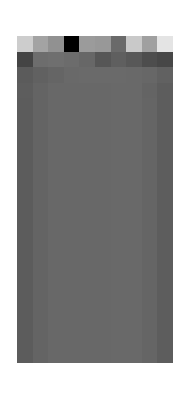

```mathematica
ArrayPlot[NestList[Code20Row,RandomReal[{0, 1}, 10],20]]
```

In particular, we can use the variance of the last row as a metric for the longevity of a solution. (e.g. a long-lived solution will have some ones and some zeros retaining high variance, while a short-lived solution or a graying-out solution will tend to average out to low variance).

### Gradient Descent

```mathematica
SingleGradientDescent[f_, steps_, d_,ogpoint_]:=Module[
{point=ogpoint,temp=0.1, prevloss=f[ogpoint], loss=f[ogpoint], gradient, prevpoint},
Do[
prevpoint=point;
gradient=(Table[f[point-d*UnitVector[Length[point], i]], {i, Length[point]}]-loss)/d;
point-=gradient*temp;
prevloss=loss;
loss=f[point];
If[prevloss>loss, point=prevpoint;temp*=0.5;,temp*=1.1];
, {step, steps}];
Return[point];
]

GradientDescent[f_, bounds_, numpoints_:1000,steps_:100, d_:10^-10]:=Module[{points=Transpose[Table[RandomReal[bound, 10*numpoints], {bound, bounds}]], threshold},

threshold=Min[f/@RandomChoice[points, 10]];
points=ParallelTable[If[f[point]<threshold, point, Nothing], {point, points}];

points=ParallelTable[SingleGradientDescent[f, steps, d, point], {point, points}];
First[MinimalBy[points, f]]]
```

### Tests

```mathematica
n=50;
GradientDescent[If[Min[#]>=0&&Max[#]<=1,-(Variance[Nest[Code20Row,#,n]]), 0]&, ConstantArray[{0, 1}, 10]]
```

{0.676676,0.921857,0.981478,0.934305,0.0893493,0.932943,0.190891,0.202291,0.84107,0.991292}

0.177745

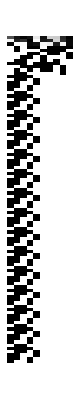

```mathematica
Variance[Nest[Code20Row,,2n]]
ArrayPlot[NestList[Code20Row,,2n]]
```

#### Conclusions

Even for very short-lifespan tests (even only two steps!!!), this technique doesn’t seem to lock on to any specific solution. It may be possible to apply an activation function for a shaper distinction between black and white to significantly improve this technique.